## Graph models: Regular, Random, Scale free (Figure 14.1) – and others that are interspersed through the Chapter

```mathematica
Clear["Global`*"];
```

```mathematica
nVert=20;
gReg=CycleGraph[nVert,VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

Grid graph

```mathematica
ggrid=GridGraph[{5,5},VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

Star graph

```mathematica
gstar=StarGraph[nVert,VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

Scale-free graph

```mathematica
SeedRandom[123];gBA=RandomGraph[BarabasiAlbertGraphDistribution[nVert,2],VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

```mathematica
dataSF=Join @@( VertexDegree /@ RandomGraph[BarabasiAlbertGraphDistribution[nVert,2],1000]);
pSF=Histogram[dataSF,{0,nVert,1},"PDF"];
```

Repeat for large graph to show power-law behavior

```mathematica
dataSF1=Join @@( VertexDegree /@ RandomGraph[BarabasiAlbertGraphDistribution[10000,2],100]);
```

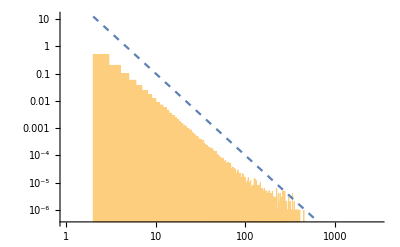

```mathematica
pSF1=Histogram[dataSF1,{0,3000,1},"PDF",ScalingFunctions->{"Log","Log"}];
Show[pSF1,LogLogPlot[100 k^-3,{k,2,600},PlotStyle->Dashed]]
```

Erdos - Rényi graph

```mathematica
SeedRandom[1]; p=4/(nVert-1);gER=RandomGraph[BernoulliGraphDistribution[nVert,p],VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

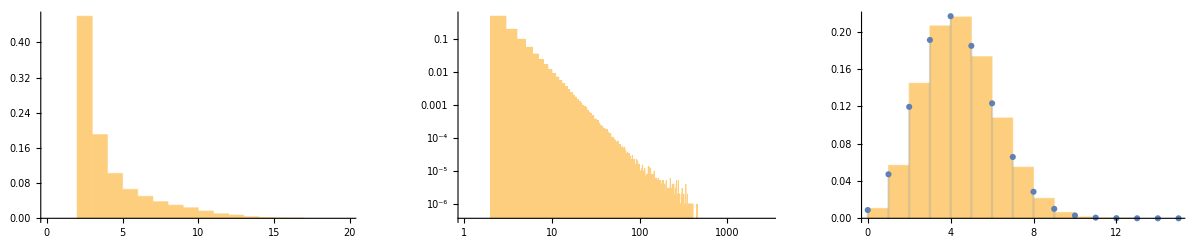

```mathematica
dataER=Join @@( VertexDegree /@ RandomGraph[BernoulliGraphDistribution[nVert,p],1000]);
pER=Show[Histogram[dataER,{0,15,1},"PDF"],DiscretePlot[PDF[BinomialDistribution[nVert,p],k]//Evaluate,{k,0,15},PlotRange->All,PlotMarkers->Automatic]];
GraphicsRow[{pSF,pSF1,pER}]
```

Note that the Binomial distribution is approximately equal to the Poisson distribution for p << 1.

Giant component in ER graph

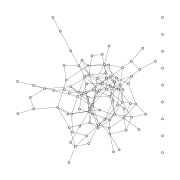

False

```mathematica
nV1=100; p=3/(nV1-1);gER1=RandomGraph[BernoulliGraphDistribution[nV1,p],VertexStyle->Directive[White,EdgeForm[Thickness[0.002]]],VertexSize->{"Scaled", 0.01},EdgeStyle->Directive[Black,Thickness[0.001]],ImageSize->Small]
ConnectedGraphQ[gER1]
```

Complete graph

```mathematica
cg=CompleteGraph[8,VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

Tree graph

```mathematica
tg=TreeGraph[Range[8],{1,1,2,1,4,2,3,1},VertexStyle->Directive[White,EdgeForm[Thickness[0.005]]],VertexSize->{"Scaled", 0.05},EdgeStyle->Directive[Black,Thickness[0.008]]];
```

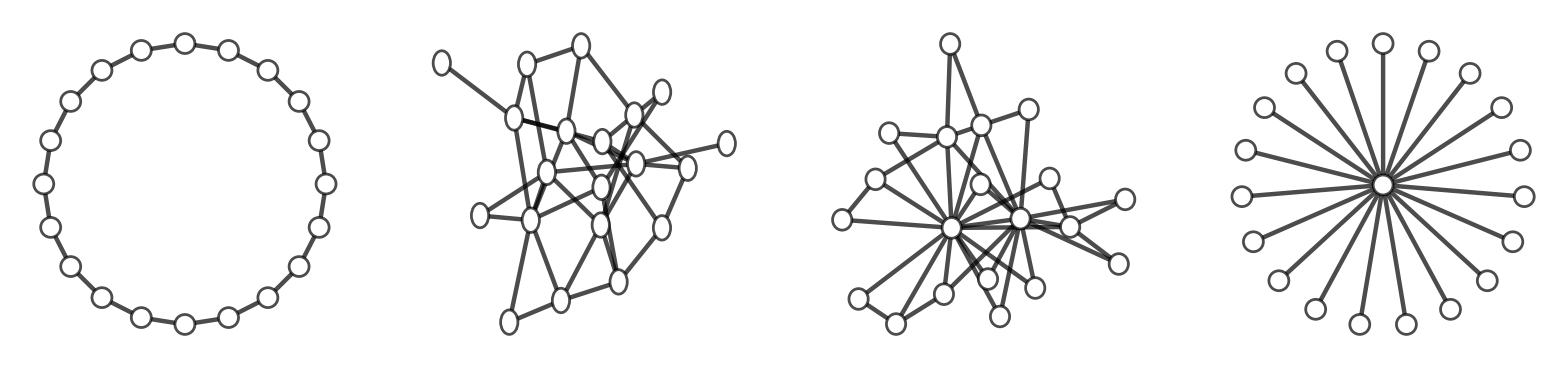

```mathematica
GraphicsRow[{gReg,gER,gBA,gstar}]
```

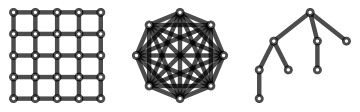

```mathematica
GraphicsRow[{ggrid,cg,tg},ImageSize->Medium]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["cyclegraph.pdf",gReg];
Export["gridgraph.pdf",ggrid];
Export["stargraph.pdf",gstar];
Export["SFvertexdegree.txt",dataSF];
Export["randomgraph.pdf",gER];
Export["scalefreegraph.pdf",gBA];
*)
```